```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/blogit"]
```

/Users/pjoot/project/figures/blogit

```mathematica
<<MaTeX`

(*See MathematicaColorToLatexRGB.nb for color mapping logic.*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor,txfonts},\definecolor{BlueDarker}{HTML}{0000AA},\definecolor{RedDarker}{HTML}{AA0000},\definecolor{PurpleDarker}{HTML}{550055},\definecolor{OrangeDarker}{HTML}{AA5500},\definecolor{GreenDarker}{HTML}{00AA00}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→16,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
ClearAll[a, alpha, z]
alpha = Exp[I Pi/3];
(z - alpha a)(z + a)(z - a/alpha)//Expand // Simplify
Integrate[1/(x^3 +a^3), {x, 0, Infinity}]
```

a^3+z^3

ConditionalExpression[(2 (1/a^3)^(2/3) π)/(3 √3), Re[a^3]≥0||a^3∉ℝ]

```mathematica
2 Pi I/(1 - alpha^2)/(z + a)/(z - a/alpha )/. z -> a alpha // Expand// FullSimplify

2Pi I/a^2/(1 - alpha^2)/(alpha+1)/(alpha - 1/alpha)// Expand // FullSimplify

-2Pi I/a^2/(alpha^2-1)^2/((alpha+1)/alpha)// Expand // FullSimplify

-2Pi I/a^2/(alpha^2-1)^2/(1 + 1/alpha)// Expand // FullSimplify
```

(2 π)/(3 √3 a^2)

(2 π)/(3 √3 a^2)

(2 π)/(3 √3 a^2)

«1 more identical outputs»

```mathematica
(1 - alpha^2)(alpha+1)(alpha - 1/alpha)//FullSimplify
```

3 ⅈ √3

```mathematica
-(1 - alpha^2)^2(alpha+1)/alpha//FullSimplify
```

3 ⅈ √3

```mathematica
-(alpha^2-1)^2(1 + 1/alpha)//FullSimplify

-(Exp[2 Pi I/3]-1)^2(1 + Exp[-I Pi/3])//FullSimplify
```

3 ⅈ √3

3 ⅈ √3

```mathematica
x = (Exp[2 Pi I/3]-1)^2//Expand//FullSimplify
y =(1 + Exp[-I Pi/3])//Expand // FullSimplify
- x y // Expand //FullSimplify
```

3/2 (1-ⅈ √3)

1-(-1)^(2/3)

3 ⅈ √3

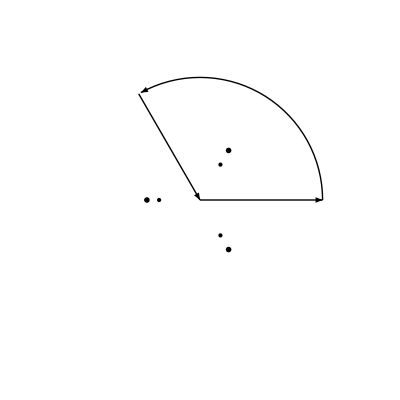

```mathematica
ClearAll[R,p1, p2, p3, line1, line2, points, labels, pieContourFig1]
R=3; (*Radius of the semicircle*)

(*Points*)
p1=Exp[I Pi/3]; (*Exp[I Pi/3]*)
p2=-1; (*-1*)
p3=Exp[-I Pi/3]; (*Exp[-I Pi/3]*)

(*Line from origin to (R,0)*)
line1=Graphics[{Thick,Arrow[{{0,0},{R,0}}]}];

(*Semicircle from (0,R) to Exp[2 I Pi/3]*)
semicircle=Graphics[{Thick,Arrow[Table[{Re[R Exp[I t]],Im[R Exp[I t]]},{t,0,2 Pi/3,Pi/50}]]}];

(*Line from Exp[2 I Pi/3] back to the origin*)
line2=Graphics[{Thick,Arrow[{{Re[R Exp[2 I Pi/3]],Im[R Exp[2 I Pi/3]]},{0,0}}]}];

(*Large points at specified locations*)
points=Graphics[{PointSize[Large],Point[{Re[p1],Im[p1]}],Point[{Re[p2],Im[p2]}],Point[{Re[p3],Im[p3]}]}];

labels = Graphics[{
Text[MaTeX["-1"], {-1.3, 0}],
Text[MaTeX["e^{i\\pi/3}"], {1, Sqrt[3]}1.4/2],
Text[MaTeX["e^{-i\\pi/3}"], {1, -Sqrt[3]}1.4/2]}];

(*Combine all graphics elements*)

pieContourFig1=Show[line1,semicircle,line2,points,labels, AspectRatio->Automatic,PlotRange->{{-R-1,R+1},{-R-1,R+1}},Axes->False,Ticks->None,Frame->False]
```

```mathematica
peeters`exportForLatex["pieContourFig1",pieContourFig1]
```

{pieContourFig1.eps,pieContourFig1pn.png}

```mathematica
t = (1/2)(1 + Sqrt[3]I)
s = (t)^2//Expand
s^2//Expand
```

1/2 (1+ⅈ √3)

-1/2+(ⅈ √3)/2

-1/2-(ⅈ √3)/2